```mathematica
q0 = 0.002;
q1 = 0.05;
q2 = 0.02;

QRestriction:=q1^(x1+1)+q2^(x2+1);
EvaluateRestriction[x1_, x2_]:=q1^(x1+1)+q2^(x2+1);

GradQ:=Grad[QRestriction, {x1,x2}];
EvaluateGradQ1[value1_]:=Assuming[x1==value1,Refine[GradQ[[1]]]];
EvaluateGradQ2[value2_]:=Assuming[x2==value2,Refine[GradQ[[2]]]];
AbsGradQ[x1_,x2_]:=Sqrt[EvaluateGradQ1[x1]^2+EvaluateGradQ2[x2]^2];

p1 = 3;
p2 = 5;

TargetF:=p1*(x1+1) + p2*(x2+1);
EvaluateTargetF[x1_, x2_]:=p1*(x1+1) + p2*(x2+1);

GradTargetF:=Grad[TargetF, {x1,x2}];
EvaluateGradTarget1[value1_]:=Assuming[x1==value1,Refine[GradTargetF[[1]]]];
EvaluateGradTarget2[value2_]:=Assuming[x2==value2,Refine[GradTargetF[[2]]]];
AbsGradF[x1_,x2_]:=Sqrt[EvaluateGradTarget1[x1]^2+EvaluateGradTarget2[x2]^2];

PrintResult[k_,init1_,init2_, x1_,x2_]:=Module[{ceil1=Ceiling[x1],ceil2=Ceiling[x2]},
Print[Row[{"Iterations",k},"="]];
Print[Row[{"Init 1st block",Row[{1,init1},"+"]},"="]];
Print[Row[{"init 2nd block",Row[{1,init2},"+"]},"="]];
Print[Row[{"Add to 1st block",x1-init1},"="]];
Print[Row[{"Add to 2nd block",x2-init2},"="]];
Print[Row[{"Solution for 1st block",Row[{x1,ceil1},"→"]},"="]];
Print[Row[{"Solution for 2nd block",Row[{x2,ceil2},"→"]},"="]];
Print[Row[{"Probability of failure",EvaluateRestriction[ceil1,ceil2]},"="]];
Print[Row[{"Power consumption",EvaluateTargetF[ceil1,ceil2]},"="]];
];
```

## Const step

#### Common

```mathematica
FindNextPoint[cur1_,cur2_,step_]:=Module[{grad1,grad2,new1,new2},
If[EvaluateRestriction[cur1,cur2]≤q0,
grad1=EvaluateGradTarget1[cur1];
grad2=EvaluateGradTarget2[cur2];,
grad1=EvaluateGradQ1[cur1];
grad2=EvaluateGradQ2[cur2];
];
new1=cur1-grad1*step;
new2=cur2-grad2*step;
Return[{new1,new2}];
];
```

#### Const step

```mathematica
FindMin[init1_,init2_,step_,ϵ_]:=Module[{k=1,cur1=init1,cur2=init2,curF,nextPoint,array,region},
curF=EvaluateTargetF[init1,init2];
nextPoint=FindNextPoint[init1,init2,step];
array={{init1,init2}};
While[Abs[cur1-nextPoint[[1]]]≥ϵ||Abs[cur2-nextPoint[[2]]]≥ϵ,
cur1=nextPoint[[1]];
cur2=nextPoint[[2]];
AppendTo[array,{cur1,cur2}];
nextPoint=FindNextPoint[cur1,cur2,step];
k++;
];
PrintResult[k,init1,init2,cur1,cur2];
region =RegionPlot[QRestriction≤q0,{x1,0,3},{x2,0,3},PlotLegends->{QRestriction}, AxesLabel->Automatic];
Show[ListPlot[array,PlotRange->{{0,3},{0,3}}],region,AspectRatio->1]
];
```

#### Spliting step

```mathematica
FindMinSplit[init1_,init2_,initStep_,ϵ_]:=Module[{k=1,cur1=init1,cur2=init2,curF,nextPoint,array,region,step,prevF},
step=initStep;
curF=EvaluateTargetF[init1,init2];
nextPoint=FindNextPoint[init1,init2,step];
array={{init1,init2}};
While[Abs[cur1-nextPoint[[1]]]≥ϵ||Abs[cur2-nextPoint[[2]]]≥ϵ,
prevF=EvaluateTargetF[cur1,cur2];
cur1=nextPoint[[1]];
cur2=nextPoint[[2]];
curF=EvaluateTargetF[cur1,cur2];
AppendTo[array,{cur1,cur2}];
nextPoint=FindNextPoint[cur1,cur2,step];
k++;
If[curF>prevF,step=initStep/Sqrt[k]];
];
PrintResult[k,init1,init2,cur1,cur2];
region =RegionPlot[QRestriction≤q0,{x1,0,3},{x2,0,3},PlotLegends->{QRestriction}, AxesLabel->Automatic];
Show[ListPlot[array,PlotRange->{{0,3},{0,3}}],region]
];
```

#### Different starting points

==Iterations1722

==Init 1st block++13

==init 2nd block++13

==Add to 1st block-1.61125

==Add to 2nd block-2.29681

==Solution for 1st block→→1.388752

==Solution for 2nd block→→0.7031941

==Probability of failure0.000525

==Power consumption19

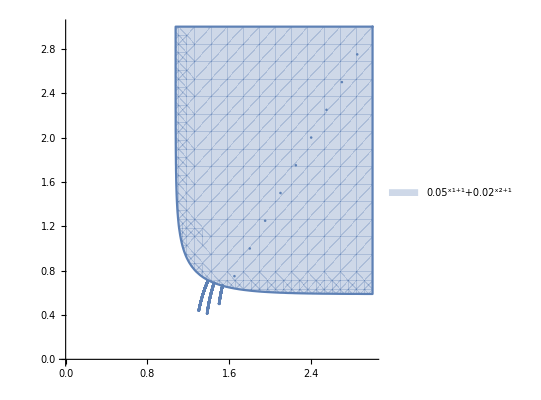

```mathematica
FindMin[3,3,0.05,0.000125]
```

==Iterations13

==Init 1st block++13

==init 2nd block++13

==Add to 1st block-1.49983

==Add to 2nd block-2.49889

==Solution for 1st block→→1.500172

==Solution for 2nd block→→0.5011051

==Probability of failure0.000525

==Power consumption19

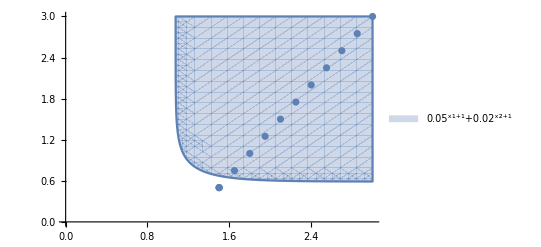

```mathematica
FindMinSplit[3,3,0.05,0.00025]
```